```mathematica
Quit[]
```

#### Get component function (temporary)

```mathematica
Needs["Olveretal`"];
ClearAll[GetComponent]
Options[GetComponent]={Coordinates->"Spherical",Mute->True};
GetComponent[solvec_List,expr_List,layer_Integer,layout_List,n_Integer,OptionsPattern[]]:=
Block[{position,subdomain,nsubdomains,partition,zeroInDomain,startindex,listParity,listExtracted,(*options*) coordinates},

(* set up options *)
coordinates=OptionValue[Coordinates];
If[!OptionValue[Mute],
If[SameQ[coordinates,"Spheroidal"],Print["Spheroidal coordinates"],Print["Spherical coordinates"]]
];

(* recover subdomains from model *)
partition=Partition[Sort(*@Rest*)[Fennec`domain],2,1];
nsubdomains=Length[partition];
Table[subdomain[i]=partition⟦i⟧,{i,1,Length[partition]}];
If[SameQ[N@First[subdomain[1]],0.],zeroInDomain=True,zeroInDomain=False];

(* find component position in solution vector *)
position=Flatten@Position[layout,Alternatives@@expr];

(* find parity of fields accross the origin based on their indices of spherical harmonics *)
listParity=
Block[{out},
If[zeroInDomain&&SameQ[layer,1],
Which[
SameQ[coordinates,"Spheroidal"],
Which[
MatchQ[#,f_[ℓ_,𝓂_]/;EvenQ[ℓ+𝓂]],out="even";,
MatchQ[#,f_[ℓ_,𝓂_]/;OddQ[ℓ+𝓂]],out="odd";,
True,Print["error with parity !"]
],
SameQ[coordinates,"Spherical"],
Which[
MatchQ[#,f_[ℓ_,𝓂_]/;EvenQ[ℓ]],out="even";,
MatchQ[#,f_[ℓ_,𝓂_]/;OddQ[ℓ]],out="odd";,
True,Print["error with parity !"];
],
True,Print["error with coordinates !"];
]
];
out
]&/@expr;

(* extracted elements from solution vector *)
listExtracted=
Block[{extracted},
If[zeroInDomain,
startindex=Max[(layer-3/2)*n*Length[layout]+1,1];
If[SameQ[layer,1],
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n/2-1⟧,{(#-1)*n/2+1,#*n/2}],
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n-1⟧,{(#-1)*n+1,#*n}]
],
startindex=(layer-1)*n*Length[layout]+1;
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n-1⟧,{(#-1)*n+1,#*n}]
]
]&/@position;

(* output: riffle with zeroes if zero is in first layer *)
If[zeroInDomain&&SameQ[layer,1],
Table[
Switch[listParity⟦i⟧,
"even",N@Riffle[listExtracted⟦i⟧,0.+0.ⅈ],
"odd",N@Riffle[listExtracted⟦i⟧,0.+0.ⅈ,{1,-1,2}],
True,Print["error with Riffle !"]
]
,{i,1,Length[expr]}],
N@listExtracted
]

]
```

Get::noopen: Cannot open Olveretal`.

Needs::nocont: Context Olveretal` was not created when Needs was evaluated.

# Inviscid Navier-Stokes + simple radial density stratification (in Boussinesq approximation)

## Load fennec & spectral package

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["spectral`","../spectral.m"];
Needs["fennec`","../fennec.m"];
```

## Components of vorticity and thermal equations

### two curls

```mathematica
rCurlCurlInertia[ℓ_,𝓂_]:=(ℓ^2 (1+ℓ)^2 P[ℓ,𝓂][r])/r^2-(2 ℓ (1+ℓ) P[ℓ,𝓂]'[r])/r-ℓ (1+ℓ) P[ℓ,𝓂]''[r];
rCurlCurlCoriolis[ℓ_,𝓂_]:=2(-(ℓ (1+2 ℓ) (-√((ℓ (-1+ℓ^2))/(-1+4 ℓ^2))+√((1-ℓ^2)/(ℓ-4 ℓ^3))) √(-((-1+ℓ^2) (ℓ-𝓂) (ℓ+𝓂))/(ℓ-4 ℓ^3)) T[-1+ℓ,𝓂][r])/r-ℓ (1+2 ℓ) √((1-ℓ^2)/(ℓ-4 ℓ^3)) √(-((-1+ℓ^2) (ℓ-𝓂) (ℓ+𝓂))/(ℓ-4 ℓ^3)) T[-1+ℓ,𝓂]'[r]-(ⅈ ℓ (1+ℓ) 𝓂 P[ℓ,𝓂][r])/r^2+(2 ⅈ 𝓂 P[ℓ,𝓂]'[r])/r+ⅈ 𝓂 P[ℓ,𝓂]''[r]-((1+ℓ) (1+2 ℓ) (√((ℓ (2+ℓ))/(3+11 ℓ+12 ℓ^2+4 ℓ^3))+√((ℓ (1+ℓ) (2+ℓ))/(3+4 ℓ (2+ℓ)))) √((ℓ (2+ℓ) (1+ℓ-𝓂) (1+ℓ+𝓂))/((1+ℓ) (1+2 ℓ) (3+2 ℓ))) T[1+ℓ,𝓂][r])/r-(1+ℓ) (1+2 ℓ) √((ℓ (2+ℓ))/(3+11 ℓ+12 ℓ^2+4 ℓ^3)) √((ℓ (2+ℓ) (1+ℓ-𝓂) (1+ℓ+𝓂))/((1+ℓ) (1+2 ℓ) (3+2 ℓ))) T[1+ℓ,𝓂]'[r]);
rCurlCurlBuoyancy[ℓ_,𝓂_]:=ℓ(ℓ+1)ϑ[ℓ,𝓂][r]
```

### one curl

```mathematica
rCurlInertia[ℓ_,𝓂_]:=ℓ (1+ℓ) T[ℓ,𝓂][r];
rCurlCoriolis[ℓ_,𝓂_]:=2(((-1+ℓ)^2 (1+ℓ) √((ℓ-𝓂) (ℓ+𝓂)) P[-1+ℓ,𝓂][r])/(r (-1+2 ℓ))-((-1+ℓ^2) √((ℓ-𝓂) (ℓ+𝓂)) P[-1+ℓ,𝓂]'[r])/(-1+2 ℓ)-(ℓ (2+ℓ)^2 √((1+ℓ-𝓂) (1+ℓ+𝓂)) P[1+ℓ,𝓂][r])/(r (3+2 ℓ))-(ℓ (2+ℓ) √((1+ℓ-𝓂) (1+ℓ+𝓂)) P[1+ℓ,𝓂]'[r])/(3+2 ℓ)-ⅈ 𝓂 T[ℓ,𝓂][r]);
rCurlBuoyancy[ℓ_,𝓂_]:=0;
```

### thermal equation

```mathematica
uGradT0[ℓ_,𝓂_]:=-ℓ(ℓ+1)P[ℓ,𝓂][r]
thermalDissipation[ℓ_,𝓂_]:=(ϑ[ℓ,𝓂]''[r]+2/r ϑ[ℓ,𝓂]'[r]-(ℓ(ℓ+1))/r^2 ϑ[ℓ,𝓂][r])
```

### putting things together

```mathematica
N2=0.5;κ=0.00;
```

```mathematica
ClearAll[eqNS1,eqNS2,eqthermal]
eqNS1[ℓ_,𝓂_]:=(ⅈ ω)rCurlCurlInertia[ℓ,𝓂]+rCurlCurlCoriolis[ℓ,𝓂]-N2 rCurlCurlBuoyancy[ℓ,𝓂]==0
eqNS2[ℓ_,𝓂_]:=(ⅈ ω)rCurlInertia[ℓ,𝓂]+rCurlCoriolis[ℓ,𝓂]-N2 rCurlBuoyancy[ℓ,𝓂]==0
eqthermal[ℓ_,𝓂_]:=(ⅈ ω)ϑ[ℓ,𝓂][r]+uGradT0[ℓ,𝓂]-κ thermalDissipation[ℓ,𝓂]==0
```

## Call to fennec

```mathematica
With[{𝓂=1,ℓmax=10},
ℒ=Flatten@Table[Simplify[{eqNS1[ℓ,𝓂],eqNS2[ℓ-1,𝓂],eqthermal[ℓ,𝓂]}],{ℓ,2,ℓmax,2}];
ℬ=Flatten@Table[{P[ℓ,𝓂][1]==0(*,ϑ[ℓ,𝓂]'[1]==0*)},{ℓ,2,ℓmax,2}];
𝒱=SortBy[Flatten@Table[{P[ℓ,𝓂],T[ℓ-1,𝓂],ϑ[ℓ,𝓂]},{ℓ,2,ℓmax,2}],Head]
];
```

```mathematica
A=FennecFun[Join[ℒ,ℬ],𝒱,{r,0,1},100,eigenvalue->ω]
```

partition of the spatial domain : {{0,1}}

regularity conditions will be enforced at r=0 based on indices of spherical harmonics

eigenvalue problem of type :  (A0+A1 ω)x==0

Size of output matrices : 750x750

{SparseArray[…],SparseArray[…]}

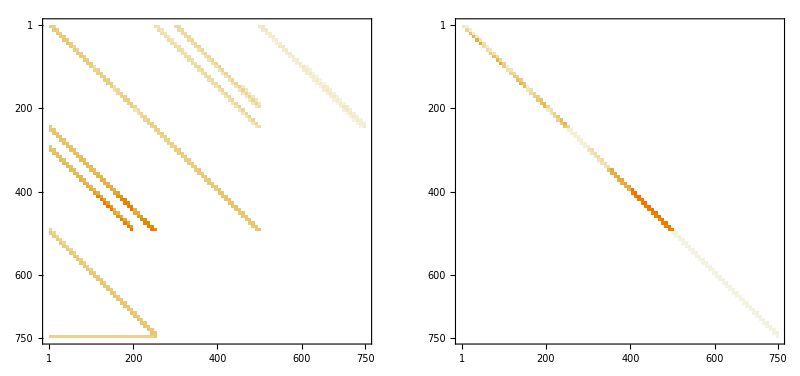

```mathematica
GraphicsRow[MatrixPlot/@Abs[A]]
```

## Solve and post-process

```mathematica
target=(*1.306078;*)(*0.611984935;*)(*0.6018079098587724-0.004710037467145376 ⅈ;*)1;
```

```mathematica
{eig,eigv}=Sort@Eigensystem[{A⟦1⟧,-A⟦2⟧}]//Chop;
eigv=Delete[eigv,Position[eig,ComplexInfinity]];
eig=Delete[eig,Position[eig,ComplexInfinity]];
pos=Nearest[eig->Automatic,target,1][[1]];
```

```mathematica
eig⟦pos⟧
eigv⟦pos⟧;
```

1.

```mathematica
(* extract components from solution *)
ClearAll[out,outnull]
Block[{list,coef,assoc=<||>},
Table[
list[layer]=Fennec`layout⟦layer⟧;
coef[layer]=Chop@GetComponent[eigv⟦pos⟧,list[layer],layer,Fennec`layout⟦layer⟧,Fennec`nr];
AppendTo[assoc,AssociationThread[list[layer],coef[layer]]]
,{layer,1,Fennec`nlayers}];
out=assoc;
]
outnull=Map[(#)->ConstantArray[0,Fennec`nr]&,Keys[out]/.f_[ℓ_,𝓂_]->f[ℓ-1,𝓂]]~Join~Map[(#)->ConstantArray[0,Fennec`nr]&,Keys[out]/.f_[ℓ_,𝓂_]->f[ℓ+1,𝓂]];
AppendTo[out,outnull];
```

```mathematica
ClearAll[NChebevalC]
NChebevalC[c_][x_]:=NChebeval[N[Re[c]]][x]+ⅈ NChebeval[N[Im[c]]][x]
xk=Cos[((2Range[1,Fennec`nr]-1)π)/(2Fennec`nr)]//N;
rk=Fennec`rfu[1][xk];
```

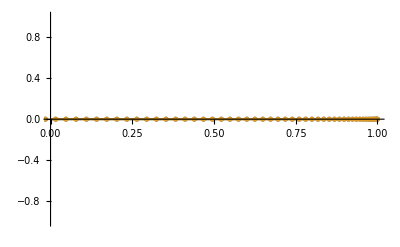

```mathematica
(* plot chosen component *)
data=NChebevalC[ϑ[2,1]/.out][rk];
interp=Interpolation[{rk,data}ᵀ];
Show[Plot[{Re[interp[r]],Im[interp[r]]},{r,0,1},PlotRange->{{0,1},All}],ListPlot[{{rk,Re[data]}ᵀ,{rk,Im[data]}ᵀ}]]
```

```mathematica
<<MaTeX`
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

1.58026

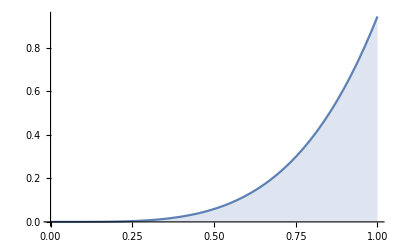

```mathematica
(* Compute angular momentum *)
dataAM=rk^3 NChebevalC[T[1,1]/.out][rk];
interpAM=Interpolation[{rk,dataAM}ᵀ];
normL=N[8/3 π NIntegrate[Re[interpAM[r]],{r,0,1}],5]
plotAM=Plot[Re[interpAM[r]],{r,0,1},Filling->Axis,PlotRange->All,PlotLabel->MaTeX["\\frac{8\\pi}{3}\\int_0^1r^3 T_{1,1}~dr="<>ToString[N[DecimalForm@normL,5]]]]
```

## Plot fields

```mathematica
ClearAll[up,ut,upint,utint,urint,ucint,upintconj,ucintconj,urintconj,utintconj,uout]
gridr=N@Subdivide[Sequence@@Fennec`layer[1],100];
Block[{mode=pos,ℓ,𝓂,head,subset=Fennec`layout⟦1⟧,listcomp,comp},
listcomp=GetComponent[(*solution*)eigv⟦mode⟧,subset,1,Fennec`layout⟦1⟧,Fennec`nr,Coordinates->"Spherical"];
Table[
head=Head[subset⟦i⟧];ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
comp=listcomp⟦i⟧;
Which[
SameQ[head,P],
up[ℓ,𝓂]=((Function[x,(NChebeval[Re@N@#][Fennec`ufr[1][x]]+ⅈ NChebeval[N@Im@#][Fennec`ufr[1][x]])]/@gridr)&@comp);
upint[ℓ,𝓂]=Interpolation[{gridr,up[ℓ,𝓂]}ᵀ];
upintconj[ℓ,𝓂]=Interpolation[{gridr,up[ℓ,𝓂]*}ᵀ];
urint[ℓ,𝓂]=Evaluate[(ℓ(ℓ+1))/# upint[ℓ,𝓂][#]]&;
urintconj[ℓ,𝓂]=Evaluate[(ℓ(ℓ+1))/# upintconj[ℓ,𝓂][#]]&;
ucint[ℓ,𝓂]=Evaluate[(upint[ℓ,𝓂][#])/#+upint[ℓ,𝓂]'[#]]&;
ucintconj[ℓ,𝓂]=Evaluate[(upintconj[ℓ,𝓂][#])/#+upintconj[ℓ,𝓂]'[#]]&,
SameQ[head,T],
ut[ℓ,𝓂]=((Function[x,(NChebeval[Re@N@#][Fennec`ufr[1][x]]+ⅈ NChebeval[N@Im@#][Fennec`ufr[1][x]])]/@gridr)&@comp);
utint[ℓ,𝓂]=Interpolation[{gridr,ut[ℓ,𝓂]}ᵀ];
utintconj[ℓ,𝓂]=Interpolation[{gridr,ut[ℓ,𝓂]*}ᵀ],
SameQ[head,ϑ],
temp[ℓ,𝓂]=((Function[x,(NChebeval[Re@N@#][Fennec`ufr[1][x]]+ⅈ NChebeval[N@Im@#][Fennec`ufr[1][x]])]/@gridr)&@comp);
tempint[ℓ,𝓂]=Interpolation[{gridr,temp[ℓ,𝓂]}ᵀ];
tempintconj[ℓ,𝓂]=Interpolation[{gridr,temp[ℓ,𝓂]*}ᵀ]
];
(*dissipation[ℓ,𝓂]=Evaluate[1/2(4π)/(2ℓ+1)Ek(ℓ(ℓ+1)Abs[urint[ℓ,𝓂][#]+# ucint[ℓ,𝓂]'[#]-ucint[ℓ,𝓂][#]]^2+ℓ(ℓ+1)Abs[# utint[ℓ,𝓂]'[#]- utint[ℓ,𝓂][#]]^2+3 Abs[# urint[ℓ,𝓂]'[#]]^2+(ℓ-1)ℓ(ℓ+1)(ℓ+2)(Abs[ucint[ℓ,𝓂][#]]^2+Abs[utint[ℓ,𝓂][#]]^2))/.parameters]&;*)

uout[-1][ℓ,𝓂]=Evaluate[√((ℓ(ℓ+1))/2)(ucint[ℓ,𝓂][#]-ⅈ utint[ℓ,𝓂][#])]&;uout[0][ℓ,𝓂]=Evaluate[urint[ℓ,𝓂][#]]&;uout[+1][ℓ,𝓂]=Evaluate[√((ℓ(ℓ+1))/2)(ucint[ℓ,𝓂][#]+ⅈ utint[ℓ,𝓂][#])]&;

,{i,1,Length[subset]}]
];
```

```mathematica
utint[ℓ_,𝓂_][r_]:=0;
urint[ℓ_,𝓂_][r_]:=0;
ucint[ℓ_,𝓂_][r_]:=0;
upint[ℓ_,𝓂_][r_]:=0;
utintconj[ℓ_,𝓂_][r_]:=0;
urintconj[ℓ_,𝓂_][r_]:=0;
ucintconj[ℓ_,𝓂_][r_]:=0;
upintconj[ℓ_,𝓂_][r_]:=0;
tempint[ℓ_,𝓂_][r_]:=0;
tempintconj[ℓ_,𝓂_][r_]:=0;
```

```mathematica
ClearAll[Y]
Y[ℓ_,𝓂_,θ_,ϕ_]:=Y[ℓ,𝓂,θ,ϕ]=√((4π)/(2 ℓ+1))SphericalHarmonicY[ℓ,𝓂,θ,ϕ]
```

```mathematica
gridθ=Range[0.,π,π/100];
Block[{ℓ,𝓂,subset=Fennec`layout⟦1⟧,ϕ=0},
gridur=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
Re@Which[
SameQ[{ℓ,𝓂},{0,0}],uout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ],
SameQ[𝓂,0],uout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ],
True,2*uout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ]
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
griduθ=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
(√2)/2 Re@Which[
SameQ[{ℓ,𝓂},{0,0}],0.+ⅈ 0.,
SameQ[𝓂,0],uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]-uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ],
True,2(uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]-uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ])
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
griduϕ=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
(√2)/2 Re@Which[
SameQ[{ℓ,𝓂},{0,0}],0.+ⅈ 0.,
SameQ[𝓂,0],uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]+uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ],
True,2(uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]+uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ])
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
(*gridDis=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
Re@Which[
SameQ[{ℓ,𝓂},{0,0}],dissipation[ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ],
SameQ[𝓂,0],dissipation[ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ],
True,2*dissipation[ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ]
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];*)
gridtemp=Chop[Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
Re@Which[
SameQ[{ℓ,𝓂},{0,0}],tempint[ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ],
SameQ[𝓂,0],tempint[ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ],
True,2*tempint[ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ]
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}],10^-6];
];
griduρ=(gridurᵀ*Sin[gridθ]+griduθᵀ*Cos[gridθ])ᵀ;
griduz=(gridurᵀ*Cos[gridθ]-griduθᵀ*Sin[gridθ])ᵀ;
```

```mathematica
coord[r_,θ_,ϕ_]:=
{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ] };
ClearAll[StreamMeridPlot,MeridPlot]
StreamMeridPlot[rj_List,θk_List,ϕ_,{v1_,v2_,s_},opts___]:=
Module[{nr=Length[rj],nθ=Length[θk],tab,max=If[Max@Abs[s]≠0,Max@Abs[s],1]},
tab=Flatten[Table[{{√((coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦1⟧)^2+(coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦2⟧)^2),coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦3⟧},{{v1⟦j,k⟧,v2⟦j,k⟧},s⟦j,k⟧}},{j,1,nr},{k,1,nθ}],1];
tab;
ListStreamDensityPlot[tab,ColorFunction->(Lighter[ColorData["ThermometerColors"][Rescale[#,{-max,max} ]],0.1]&),ColorFunctionScaling->False,opts]]
coord[r_,θ_,ϕ_]:=
{Abs[r] Cos[ϕ] Sin[θ],Abs[r] Sin[θ] Sin[ϕ],Abs[r] Cos[θ] };
MeridPlot[rj_List,θk_List,mat_,ϕ_,opts___]:=
Module[{nr=Length[rj],nθ=Length[θk],tab,max=If[Max@Abs[mat]≠0,Max@Abs[mat],1]},
tab=Flatten[Table[{Sign[rj⟦j⟧] √((coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦1⟧)^2+(coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦2⟧)^2),coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦3⟧,mat⟦j,k⟧},{j,1,nr},{k,1,nθ}],1];
ListContourPlot[tab,ColorFunction->(ColorData["ThermometerColors"][Rescale[#,{-max,max} ]]&),ColorFunctionScaling->False,opts]]
```

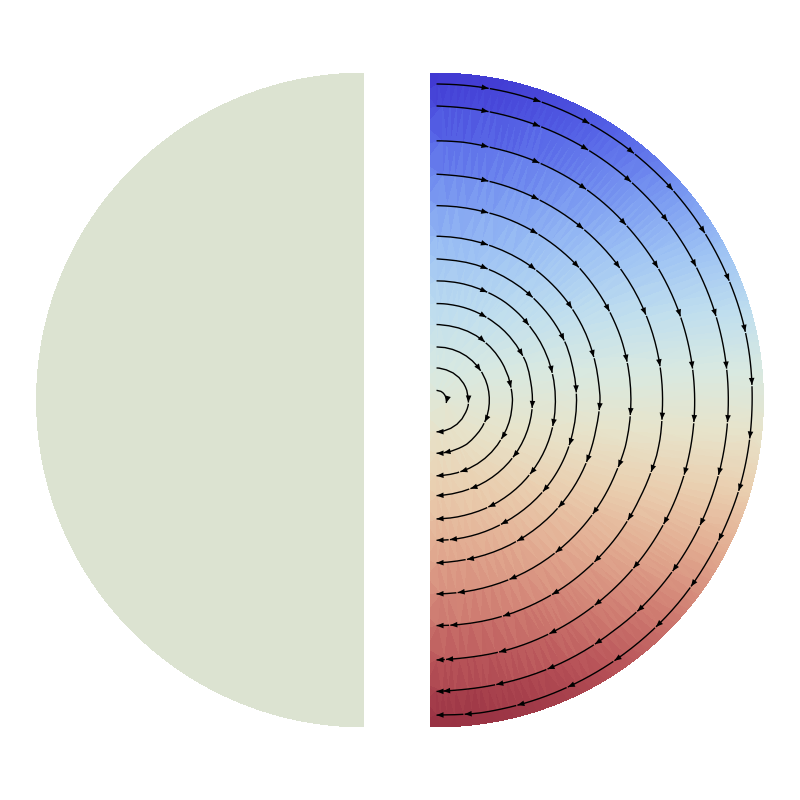

```mathematica
plot=Show[
GraphicsGrid[{{
Show[MeridPlot[-gridr,gridθ,gridtemp,0,AspectRatio->2,PlotRangePadding->None,Frame->False,Contours->20,PlotRange->All,ContourStyle->None,RegionFunction->Function[{x,y,z},First[Fennec`domain]<Norm[{x,y}]<Last[Fennec`domain]]],PlotLabel->MaTeX["\\text{Temperature}",Magnification->1]],
Show[StreamMeridPlot[gridr,gridθ,0,{griduρ,griduz,griduϕ},AspectRatio->2,PlotRangePadding->None,Frame->False,PlotRange->All,StreamScale->Medium,StreamStyle->Black,RegionFunction->Function[{x,y,z},First[Fennec`domain]<Norm[{x,y}]<Last[Fennec`domain]]],PlotLabel->MaTeX["\\text{Velocity}",Magnification->1]]}},Spacings->0],PlotLabel->MaTeX["\\omega="<>ToString[ω/.(*parameters*)ω->Chop@N[eig⟦pos⟧,5]],Magnification->1.5]]
```

```mathematica
export=GraphicsRow[{plot,plotAM},Spacings->0,ImageSize->Full]
```

-Graphics-

```mathematica
Export["~/Desktop/gravito-inertial modes/spin-over.pdf",export,ImageSize->1000,ImageResolution->600]
```

~/Desktop/gravito-inertial modes/spin-over.pdf